## cylindrical nanoscale mosfet compact model -- DIBL effect

### physical parameter

```mathematica
e=1.60218 10^-19;(*unit charge[C]*)
kB=1.38066 10^-23;(*Boltzmann constant[J/K]*)h=6.62607 10^-34;(*Planck's constant[Js]*)
hbar=h/(2 π);(*[Js]*)
T=300;(*temperature[K]*)
ϵ0=8.85418 10^-12;(*permittivity in vaccum[F/m]*)vt=(kB T)/e;(*thermal voltage[V]*)
m0=9.10938 10^-31;(*effective mass of electron in vaccum[kg]*)nm=10^-9;
ϵox=3.9 ϵ0;(*permittivity of oxide[F/m]*)
ϵsi=11.8 ϵ0;(*permittivity of silicon according to SILVACO[F/m]*)mt=0.19 m0;(*transverse effective mass of electron in SILICON[kg]*)
ml=0.916 m0;(*longitudinal effective mass of electron in SILICON[kg]*)
mr=2 (ml^-1+mt^-1)^-1;(*effective mass along radius direction in cross section in SILICON[kg]*)
GWF=4.5;(*workfunction of gate material from SILVACO[eV]*)CEA=4.17;(*electron affinity of channel material from SILVACO[eV]*)
wgc=GWF-CEA;(*workfunction difference between gate and channel[V]*)
wfb=0;(*conduction band edge under flat-band condition*)vbi=0.21;(*built-in voltage*)
Eg=0.54;(*fitting parameter*)
```

### device parameter

```mathematica
R=2 nm;(*radius of cross-section*)
Tox=0.5 nm;(*oxide thickness*)Cox[r_,tox_]:=2 π (ϵox)/Log[1+tox/r];(*capacitance of cylinder per unit length (F/m)*)
L1=5 nm;
L2=7 nm;
L3=10 nm;
L4=12 nm;
L=7 nm;(*Length of channel*)
```

### bias parameter

```mathematica
VGS0=0;
VGS2=0.2;
VGS5=0.5;
VGS8=0.8;
VDS=0.6;
```

### subband parameter

```mathematica
besselenergylevel[nf_,nr_,m_,r_]:=hbar^2/(2 m) (BesselJZero[nf,nr]/r)^2
besselelement[νf_,νr_,nf_,nr_]:=1/(2 Pi) Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ]^2 ζ,{ζ,0,1}]^-.5 Integrate[BesselJ[nf,BesselJZero[nf,nr] ζ]^2 ζ,{ζ,0,1}]^-.5 Integrate[Exp[I (nf-νf) ϕ],{ϕ,0,2 Pi}] Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ] (1-ζ^2) BesselJ[nf,BesselJZero[nf,nr] ζ] ζ,{ζ,0,1}]
valleykxky=4;(*4-fold degeneracy*)valleykz=2;(*2-fold degeneracy*)subbandtable={{valleykxky,mt/m0,besselenergylevel[0,1,mr,R]/e,besselenergylevel[0,1,mr,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,1,mt,R]/e,besselenergylevel[0,1,mt,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,1,mr,R]/e,besselenergylevel[1,1,mr,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,1,mt,R]/e,besselenergylevel[1,1,mt,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[0,2,mr,R]/e,besselenergylevel[0,2,mr,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,2,mt,R]/e,besselenergylevel[0,2,mt,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,2,mr,R]/e,besselenergylevel[1,2,mr,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[1,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,2,mt,R]/e,besselenergylevel[1,2,mt,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[2,2,mr,R]/e,besselenergylevel[2,2,mr,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[2,2,mt,R]/e,besselenergylevel[2,2,mt,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mt,R]/e}}(*gnv,mc,Eq0/e,Eq0/kBT,H0xx,reflection*)
```

{{4,0.19,0.175027,6.77031,0.781943,0,0.175027},{2,0.916,0.289918,11.2145,0.781943,0,0.289918},{4,0.19,0.444347,17.188,0.666667,0,0.444347},{2,0.916,0.736026,28.4706,0.666667,0,0.736026},{4,0.19,0.922208,35.6724,0.688545,0,0.922208},{2,0.916,1.52756,59.0884,0.688545,0,1.52756},{4,0.19,1.48959,57.6195,0.666667,0,1.48959},{2,0.916,2.46738,95.4421,0.666667,0,1.52756},{4,0.19,2.14426,82.9433,0.638438,0,2.14426},{2,0.916,3.5518,137.389,0.638438,0,3.5518}}

### Fermi Integral

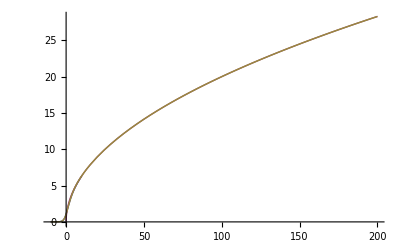

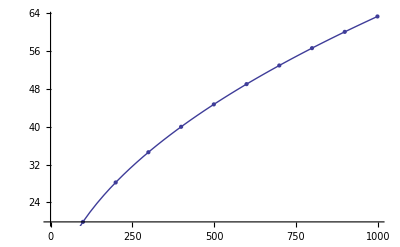

```mathematica
fermiintegral[j_,ζ_]:=-Gamma[1+j] PolyLog[1+j,-Exp[ζ]]
fermiintegralappro[j_,ζ_]:=1/(j+1) ζ^(j+1)
fermiintegralaymerich[j_,ξ_]:=(((j+1) 2^(j+1))/(b+ξ+(Abs[ξ-b]^c+a^c)^(1/c))^(j+1)+Exp[-ξ]/Gamma[j+1])^-1/.a->(1+15/4 (j+1)+1/40 (j+1)^2)^(1/2)/.b->1.8+0.61 j/.c->2+(2-Sqrt[2]) 2^-j
Plot[{fermiintegral[-0.5,x],fermiintegralappro[-.5,x],fermiintegralaymerich[-.5,x]},{x,-10,200}]
Show[ListPlot[Table[{x,fermiintegralappro[-.5,x]},{x,-1,1000,100}]],Plot[fermiintegralaymerich[-.5,x],{x,-1,1000}]]
```

## potential distribution along channel

### characteristic parameter for Bessel function

```mathematica
Cr=Cox[R,Tox]/(2 π ϵsi);
FindRoot[BesselJ[1,Λ]/BesselJ[0,Λ] Λ==Cr,{Λ,{2,3,6,10}}];
λ1=Max[FindRoot[BesselJ[1,Λ]/BesselJ[0,Λ] Λ==Cr,{Λ,{1}}][[1]][[2]]];
γ=Sqrt[4/α]/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2;
ugzero[vbi_,vgs_]:=(vbi-vgs+wgc-wfb)/-(α/R^2)/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2
ugLg[vbi_,vgs_,vds_]:=(vbi-vgs+wgc-wfb+vds)/-(α/R^2)/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2
```

### characteristic function along channel

```mathematica
s[z_]:=Exp[-λ1/R z]+(1-Exp[-λ1/R L]) Sinh[λ1/R z]/Sinh[λ1/R L]
```

### ΔUG along channel

```mathematica
ug[vbi_,vgs_,vds_,z_]:=1/Sinh[γ L] (ugzero[vbi,vgs] Sinh[γ (L-z)]+ugLg[vbi,vgs,vds] Sinh[γ z])
aug[vbi_,vgs_,vds_,z_]:=-(vbi-vgs+wgc-wfb) (Sinh[γ (L-z)]+Sinh[γ z])/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))-vds Sinh[γ z]/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))
Maug[vbi_,vgs_,vds_,z_]:=If[Re[aug[vbi,vgs,vds,z]]≤0,Re[aug[vbi,vgs,vds,z]],0]
```

### 1st energy level

```mathematica
Eq01[vbi_,vgs_,vds_,z_]:=-e WS+kB T subbandtable[[1,4]]+subbandtable[[1,5]] e ug[vbi,vgs,vds,z]/.WS->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] ug[vbi,vgs,vds,z]
```

### barrier top

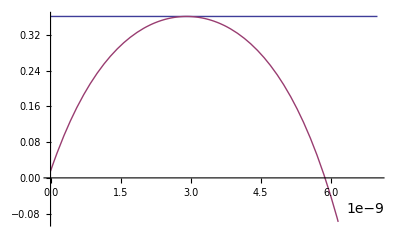

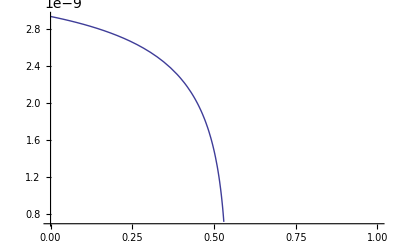

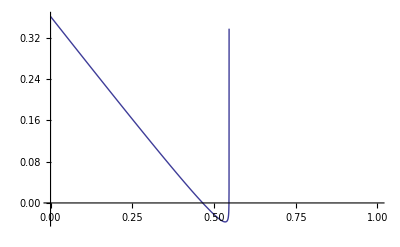

```mathematica
zmax[vbi_,vgs_,vds_]:=-1/(2 γ) Log[B/A]/.A->ugzero[vbi,vgs]/(2 Sinh[γ L]) Exp[γ L]+ugLg[vbi,vgs,vds]/(2 Sinh[γ L])/.B->ugzero[vbi,vgs]/(2 Sinh[γ L]) Exp[-γ L]+ugLg[vbi,vgs,vds]/(2 Sinh[γ L])
Plot[{Eq01[vbi,VGS0,VDS,zmax[vbi,VGS0,VDS]]/e,Eq01[vbi,VGS0,VDS,z]/e},{z,0,L}]
Plot[zmax[vbi,vgs,VDS],{vgs,0,1}]
Plot[Eq01[vbi,vgs,VDS,zmax[vbi,vgs,VDS]]/e,{vgs,0,1}]
```

### smoothing funtion

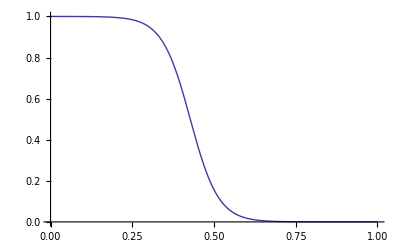

```mathematica
SF[vgs_]:=(1+Exp[μ ((e (vgs-wgc+wfb))/(kB T)-subbandtable[[1,4]]-ν)])^-1/.μ->0.6/.ν->-3
Plot[SF[vgs],{vgs,0,1}]
```

### DIBL effect involved ΔUG expression

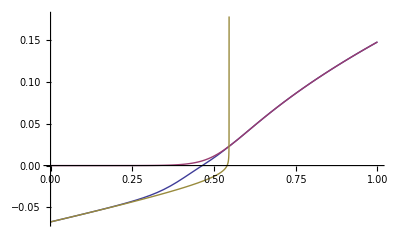

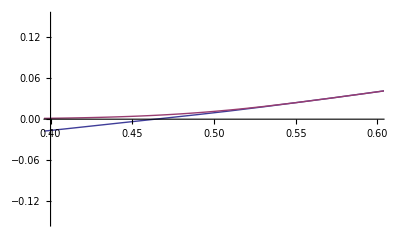

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\diblug.txt".

```mathematica
DIBLUG[vbi_,vgs_,vds_]:=Re[SF[vgs] Maug[vbi,vgs,vds,zmax[vbi,vgs,vds]]]+U[vgs]
U[vgs_]:=b/(2 a) (-1+Sqrt[1+(4 a)/(b b) 1/25 Log[1+Exp[25 (vgs+c)]]])/.a->(8 Pi^4 hbar^2 ϵsi^2)/(subbandtable[[1,1]]^2 e^3 mt)/.b->subbandtable[[1,5]]+(4 Pi ϵsi)/(Cox[R,Tox])/.c->-wgc+wfb-subbandtable[[1,3]]
Plot[{DIBLUG[vbi,vgs,VDS],U[vgs],aug[vbi,vgs,VDS,zmax[vbi,vgs,VDS]]},{vgs,0,1}(*,PlotRange->{{0.4,0.6},{-0.15,0.15}}*)]
Plot[{DIBLUG[vbi,vgs,VDS],U[vgs]},{vgs,0,1},PlotRange->{{0.4,0.6},{-0.15,0.15}}]
Export["/home/tei/mathematica/diblug.txt",Table[Re[{vgs,DIBLUG[vbi,vgs,VDS],U[vgs],Maug[vbi,vgs,VDS,zmax[vbi,vgs,VDS]]}],{vgs,0,1,0.01}],"CSV"];
```

```mathematica
Export["E:\data_for_mathematica\\diblenergyplotidsL20nm.txt",Table[Re[{vgs,Eq01[vbi,vgs,VDS,zmax[vbi,vgs,VDS]]/e}],{vgs,0,1,0.01}],"CSV"]
```

E:\data_for_mathematica\diblenergyplotidsL20nm.txt

## DIBL effect Current

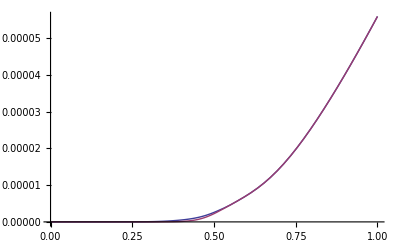

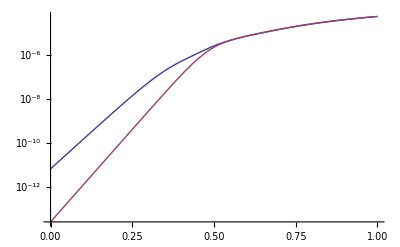

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\diblcurrentplotidsvgs.txt".

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\nodiblcurrentplotidsvgs.txt".

```mathematica
DIBLSINGLEBANDCURRENT[vbi_,vgs_,vds_,st_]:=Re[(e kB T)/(Pi hbar) st[[1,1]] (Log[1+Exp[1/vt (vgs-wgc+wfb-(4 Pi ϵsi DIBLUG[vbi,vgs,vds])/Cox[R,Tox])-st[[1,4]]-st[[1,5]]/vt DIBLUG[vbi,vgs,vds]]]-Log[1+Exp[1/vt (vgs-wgc+wfb-(4 Pi ϵsi DIBLUG[vbi,vgs,vds])/Cox[R,Tox])-st[[1,4]]-st[[1,5]]/vt DIBLUG[vbi,vgs,vds]-vds/vt]])]
WITHOUTDIBLSINGLEBANDCURRENT[vgs_,vds_,r_,tox_,st_]:=Re[(e kB T)/(Pi hbar) st[[1,1]] (Log[1+Exp[1/vt (vgs-wgc+wfb-(4 Pi ϵsi U[vgs])/Cox[R,Tox])-st[[1,4]]-st[[1,5]]/vt U[vgs]]]-Log[1+Exp[1/vt (vgs-wgc+wfb-(4 Pi ϵsi U[vgs])/Cox[R,Tox])-st[[1,4]]-st[[1,5]]/vt U[vgs]-vds/vt]])]
Plot[{DIBLSINGLEBANDCURRENT[vbi,vgs,VDS,subbandtable],WITHOUTDIBLSINGLEBANDCURRENT[vgs,VDS,R,Tox,subbandtable]},{vgs,0,1}]
LogPlot[{DIBLSINGLEBANDCURRENT[vbi,vgs,VDS,subbandtable],WITHOUTDIBLSINGLEBANDCURRENT[vgs,VDS,R,Tox,subbandtable]},{vgs,0,1}]
Export["/home/tei/mathematica/diblcurrentplotidsvgs.txt",Table[Re[{vgs,DIBLSINGLEBANDCURRENT[vbi,vgs,VDS,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
Export["/home/tei/mathematica/nodiblcurrentplotidsvgs.txt",Table[Re[{vgs,WITHOUTDIBLSINGLEBANDCURRENT[vgs,VDS,R,Tox,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
Export["E:\data_for_mathematica\\diblcurrentplotidsvgsL7.txt",Table[Re[{vgs,DIBLSINGLEBANDCURRENT[vbi,vgs,VDS,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
```

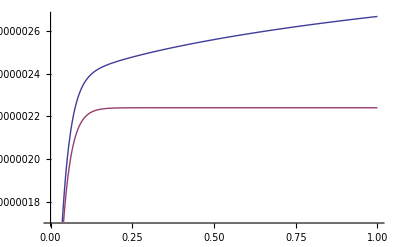

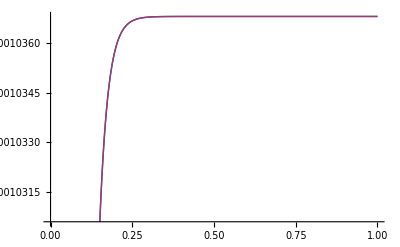

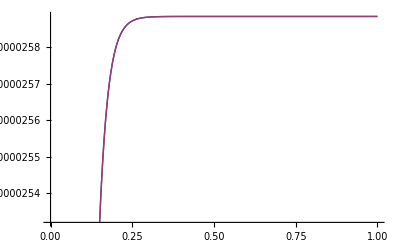

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\diblcurrentplotidsvds050.txt".

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\diblcurrentplotidsvds075.txt".

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\diblcurrentplotidsvds100.txt".

```mathematica
Plot[{DIBLSINGLEBANDCURRENT[vbi,0.5,vds,subbandtable],WITHOUTDIBLSINGLEBANDCURRENT[0.5,vds,R,Tox,subbandtable]},{vds,0,1}]
Plot[{DIBLSINGLEBANDCURRENT[vbi,0.65,vds,subbandtable],WITHOUTDIBLSINGLEBANDCURRENT[0.65,vds,R,Tox,subbandtable]},{vds,0,1}]
Plot[{DIBLSINGLEBANDCURRENT[vbi,0.8,vds,subbandtable],WITHOUTDIBLSINGLEBANDCURRENT[0.8,vds,R,Tox,subbandtable]},{vds,0,1}]
Export["/home/tei/mathematica/diblcurrentplotidsvds050.txt",Table[Re[{vds,DIBLSINGLEBANDCURRENT[vbi,0.5,vds,subbandtable]}],{vds,0,1,0.01}],"CSV"];
Export["/home/tei/mathematica/diblcurrentplotidsvds075.txt",Table[Re[{vds,DIBLSINGLEBANDCURRENT[vbi,0.65,vds,subbandtable]}],{vds,0,1,0.01}],"CSV"];
Export["/home/tei/mathematica/diblcurrentplotidsvds100.txt",Table[Re[{vds,DIBLSINGLEBANDCURRENT[vbi,0.8,vds,subbandtable]}],{vds,0,1,0.01}],"CSV"];
```

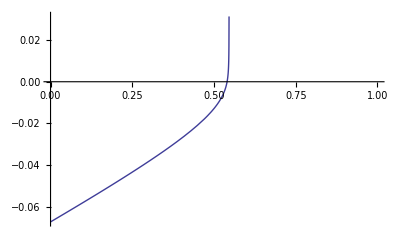

```mathematica
Plot[aug[vbi,vgs,VDS,zmax[vbi,vgs,VDS]],{vgs,0,1}]
```

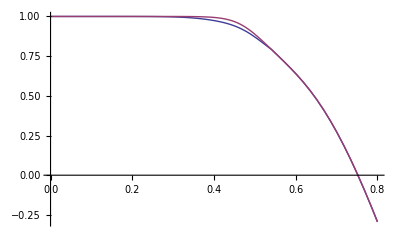

```mathematica
outputbibl[vgs_]:=VDD-DIBLSINGLEBANDCURRENT[vbi,vgs,VDS,subbandtable] r/.VDD->1/.r->50000
outputnodibl[vgs_]:=VDD-WITHOUTDIBLSINGLEBANDCURRENT[vgs,VDS,R,Tox,subbandtable] r/.VDD->1/.r->50000
Plot[{outputbibl[vgs],outputnodibl[vgs]},{vgs,0,0.8}]
```

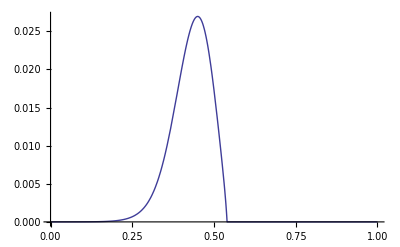

```mathematica
Plot[-outputbibl[vgs]+outputnodibl[vgs],{vgs,0,1}]
```

## HSPICE simulation

```mathematica
vt
```

0.0258522

```mathematica
Cox[R,Tox]
```

9.72318×10^-10

```mathematica
8 Pi^4 hbar^2 ϵsi^2/(4^2 e^3 mt)
```

8.30627

```mathematica
4 Pi ϵsi/Cox[R,Tox]+subbandtable[[1,5]]
```

2.13225

```mathematica
wgc+subbandtable[[1,3]]
```

0.505027

```mathematica
(8 Pi^4 hbar^2 ϵsi^2)/(subbandtable[[1,1]]^2 e^3 mt)
subbandtable[[1,5]]+(4 Pi ϵsi)/(Cox[R,Tox])
-wgc+wfb-subbandtable[[1,3]]
```

8.30627

2.13225

-0.505027

```mathematica
Sqrt[4/α]/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2
((4 π ϵsi)/Cox[R,Tox]+1) R^2
```

6.52286×10^8

9.40122×10^-18

```mathematica
ugzero[vbi,vgs]/(2 Sinh[γ L]) Exp[γ L]+ugLg[vbi,vgs,vds]/(2 Sinh[γ L])
ugzero[vbi,vgs]/(2 Sinh[γ L]) Exp[-γ L]+ugLg[vbi,vgs,vds]/(2 Sinh[γ L])
```

-0.425523 (0.54-vgs)-0.00442521 (0.54+vds-vgs)

-0.0000460198 (0.54-vgs)-0.00442521 (0.54+vds-vgs)

```mathematica
ugzero[vbi,vgs]
ugLg[vbi,vgs,vds]
```

-0.425477 (0.54-vgs)

-0.425477 (0.54+vds-vgs)

```mathematica
zmax[vbi,vgs,vds]
```

-7.66535×10^-10 Log[(-0.0000460198 (0.54-vgs)-0.00442521 (0.54+vds-vgs))/(-0.425523 (0.54-vgs)-0.00442521 (0.54+vds-vgs))]

```mathematica
aug[vbi,vgs,vds,z]
```

-0.00885042 vds Sinh[6.52286×10^8 z]+0.00885042 (-0.54+vgs) (Sinh[6.52286×10^8 (7/1000000000-z)]+Sinh[6.52286×10^8 z])

```mathematica
Eq01[vbi,vgs,vds,z]
```

2.80425×10^-20+2.606×10^-21 (-0.425477 (0.54-vgs) Sinh[6.52286×10^8 (7/1000000000-z)]-0.425477 (0.54+vds-vgs) Sinh[6.52286×10^8 z])-1.60218×10^-19 (-0.33+vgs-0.0280879 (-0.425477 (0.54-vgs) Sinh[6.52286×10^8 (7/1000000000-z)]-0.425477 (0.54+vds-vgs) Sinh[6.52286×10^8 z]))

```mathematica
-e WS+kB T subbandtable[[1,4]]+subbandtable[[1,5]] e ug/.WS->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] ug
```

2.80425×10^-20+1.25281×10^-19 ug-1.60218×10^-19 (-0.33-1.3503 ug+vgs)

```mathematica
(e kB T)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt (vgs-wgc+wfb-(4 Pi ϵsi ug)/Cox[R,Tox])-subbandtable[[1,4]]-subbandtable[[1,5]]/vt ug]]-Log[1+Exp[1/vt (vgs-wgc+wfb-(4 Pi ϵsi ug)/Cox[R,Tox])-subbandtable[[1,4]]-subbandtable[[1,5]]/vt ug-vds/vt]])
```

8.01223×10^-6 (Log[1+ⅇ^(-6.77031-30.2467 ug+38.6815 (-0.33-1.3503 ug+vgs))]-Log[1+ⅇ^(-6.77031-30.2467 ug-38.6815 vds+38.6815 (-0.33-1.3503 ug+vgs))])

```mathematica
kB T subbandtable[[1,4]]+subbandtable[[1,5]] e ug
```

2.80425×10^-20+1.25281×10^-19 ug

```mathematica
SF[vgs] Maug[vbi,vgs,vds,zmax[vbi,vgs,vds]]+U[vgs]
```

If[Re[0.00885042 (-0.54+vgs) (Sinh[6.52286×10^8 (7/1000000000+7.66535×10^-10 Log[(-0.0000460198 (0.54-vgs)-0.00442521 (0.54+vds-vgs))/(-0.425523 (0.54-vgs)-0.00442521 (0.54+vds-vgs))])]-Sinh[0.5 Log[(-0.0000460198 (0.54-vgs)-0.00442521 (0.54+vds-vgs))/(-0.425523 (0.54-vgs)-0.00442521 (0.54+vds-vgs))]])+0.00885042 vds Sinh[0.5 Log[(-0.0000460198 (0.54-vgs)-0.00442521 (0.54+vds-vgs))/(-0.425523 (0.54-vgs)-0.00442521 (0.54+vds-vgs))]]]≤0,Re[aug[0.21,vgs,vds,-7.66535×10^-10 Log[(-0.0000460198 (0.54-vgs)-0.00442521 (0.54+vds-vgs))/(-0.425523 (0.54-vgs)-0.00442521 (0.54+vds-vgs))]]],0]/(1+ⅇ^(0.6 (-3.77031+38.6815 (-0.33+vgs))))+0.128352 (-1+√(1+0.292315 Log[1+ⅇ^(25 (-0.505027+vgs))]))

```mathematica
aug[vbi,vgs,VDS,zmax[vbi,vgs,VDS]]
```

0.00885042 (-0.54+vgs) (Sinh[6.52286×10^8 (7/1000000000+7.66535×10^-10 Log[(-0.0000460198 (0.54-vgs)-0.00442521 (1.14-vgs))/(-0.425523 (0.54-vgs)-0.00442521 (1.14-vgs))])]-Sinh[0.5 Log[(-0.0000460198 (0.54-vgs)-0.00442521 (1.14-vgs))/(-0.425523 (0.54-vgs)-0.00442521 (1.14-vgs))]])+0.00531025 Sinh[0.5 Log[(-0.0000460198 (0.54-vgs)-0.00442521 (1.14-vgs))/(-0.425523 (0.54-vgs)-0.00442521 (1.14-vgs))]]

```mathematica
Plot[aug[vbi,vgs,VDS,zmax[vbi,vgs,VDS]],{vgs,0,1}]
```

-Graphics-

```mathematica
FindRoot[aug[vbi,vgs,VDS,zmax[vbi,vgs,VDS]]==0,{vgs,0.4}]
```

{vgs→0.54+1.0556×10^-17 ⅈ}

```mathematica
TraditionalForm[-(vbi-vgs+wgc-wfb) (Sinh[γ (L-z)]+Sinh[γ z])/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))-vds Sinh[γ z]/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))]
```

0.00885042 (vgs-0.54) (sinh(6.52286×10^8 (7/1000000000-z))+sinh(6.52286×10^8 z))-0.00885042 vds sinh(6.52286×10^8 z)

```mathematica
TraditionalForm[1/(2 γ) Log[AA/B]/.AA->ugzero[vbi,vgs]/(2 Sinh[γ L]) Exp[γ L]+ugLg[vbi,vgs,vds]/(2 Sinh[γ L])/.B->ugzero[vbi,vgs]/(2 Sinh[γ L]) Exp[-γ L]+ugLg[vbi,vgs,vds]/(2 Sinh[γ L])]//Simplify
```

7.66535×10^-10 log((1. vds-97.1588 vgs+52.4657)/(1. vds-1.0104 vgs+0.545616))

```mathematica
TraditionalForm[-(vbi-vgs+wgc-wfb) (Sinh[γ (L-zmax[vbi,vgs,vds])]+Sinh[γ zmax[vbi,vgs,vds]])/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))-vds Sinh[γ zmax[vbi,vgs,vds]]/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))]//Simplify
```

(0.00885042 vds+0.416718 vgs-0.225028) sinh(0.5 log((1. vds-1.0104 vgs+0.545616)/(1. vds-97.1588 vgs+52.4657)))+(0.425477 vgs-0.229757) cosh(0.5 log((1. vds-1.0104 vgs+0.545616)/(1. vds-97.1588 vgs+52.4657)))

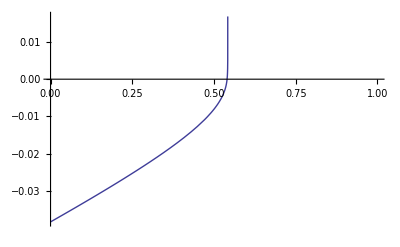

```mathematica
Plot[(0.0024007789526401305 vds+0.4230827661149983 vgs-0.2284646937020991) Sinh[0.5 Log[(1. vds-1.002821258412304 vgs+0.541523479542644)/(1. vds-355.45175657744824 vgs+191.94394855182205)]]+(0.4254767718498222 vgs-0.229757456798904) Cosh[0.5 Log[(1. vds-1.002821258412304 vgs+0.541523479542644)/(1. vds-355.45175657744824 vgs+191.94394855182205)]]/.vds->0.8,{vgs,0,1}]
```

```mathematica
Table[{(0.0024007789526401305 vds+0.4230827661149983 vgs-0.2284646937020991) Sinh[0.5 Log[(1. vds-1.002821258412304 vgs+0.541523479542644)/(1. vds-355.45175657744824 vgs+191.94394855182205)]]+(0.4254767718498222 vgs-0.229757456798904) Cosh[0.5 Log[(1. vds-1.002821258412304 vgs+0.541523479542644)/(1. vds-355.45175657744824 vgs+191.94394855182205)]]/.vds->0.8,{vgs,0,1}},{vgs,0,1,0.1}]
```

{{-0.0382926,{0.,0,1}},{-0.0332374,{0.1,0,1}},{-0.0279957,{0.2,0,1}},{-0.0224372,{0.3,0,1}},{-0.0162401,{0.4,0,1}},{-0.00804951,{0.5,0,1}},{2.05212×10^-20+0.00969524 ⅈ,{0.6,0,1}},{9.42656×10^-21+0.0145511 ⅈ,{0.7,0,1}},{4.68479×10^-21+0.0169974 ⅈ,{0.8,0,1}},{1.25924×10^-21+0.0180408 ⅈ,{0.9,0,1}},{-1.90104×10^-21+0.0179279 ⅈ,{1.,0,1}}}